```mathematica
rep[x_Integer,y_Integer,z_Integer]:=ArrayPlot[PadLeft[IntegerDigits[NestList[(FromDigits[Sort[IntegerDigits[IntegerReverse[#]+#]]])&,x,y],z]]]
```

```mathematica
rep[794,100,2]
```

-Graphics-

```mathematica
repgraph[x_Integer,y_Integer]:=NestGraph[(FromDigits[Sort[IntegerDigits[IntegerReverse[#]+#]]])&,x,y,VertexLabels->"Name"]
```

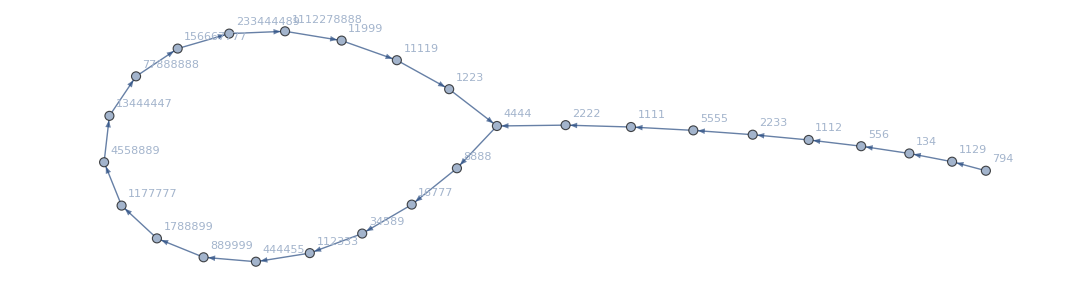

```mathematica
repgraph[794,100]
```

```mathematica
pal[x_Integer,y_Integer,z_Integer]:=ArrayPlot[PadLeft[IntegerDigits[NestWhileList[(FromDigits[Sort[IntegerDigits[IntegerReverse[#]+#]]])&,x,IntegerDigits[IntegerReverse[#,2],2]=!=IntegerDigits[#,2]&,1,y],z]]]
```

```mathematica
pal[1997,100,2]
```

-Graphics-